# Hydrogen Structure ( Result )

```mathematica
e=1.60217646 10^-19 ;(* Coulumb *)
ϵ0 = 8.854187817 10^-12;
ℏ=1.054571628 10^-34 ;(* J s*)
me = 9.10938188 10^-31 ;(* kg *)
c = 299792458;
mp=1.672621637 10^-27 ;
gp=5.585694713;
ge=2.00231904622;
α=e^2/((4π ϵ0)ℏ c)
μ0=1/(ϵ0 c^2);
μB= (e ℏ)/(2 me);
μN=(e ℏ)/(2mp);
NA=6.02214199 10^23;
```

0.00729735

```mathematica
(* Bohr radiu *)
a=ℏ/(me c α)
```

5.29177×10^-11

```mathematica
(* wavelength convertor in nm*)
λ[eV_]:=c/(eV e/(ℏ 2π)) 10^9
```

## Bohr Model

```mathematica
EBohr[n_]:=-1/2 me α^2 c^2 1/n^2 1/e (* in eV *)
```

```mathematica
Table[EBohr[n],{n,1,4}]
```

{-13.6057,-3.40142,-1.51174,-0.850356}

```mathematica
Table[λ[EBohr[m]-EBohr[n]],{n,2,3},{m,n+1,10}]//TableForm
```

656.112 | 486.009 | 433.937 | 410.07 | 396.907 | 388.807 | 383.442 | 379.695
1874.61 | 1281.47 | 1093.52 | 1004.67 | 954.345 | 922.658 | 901.253 |

```mathematica
Table[λ[EBohr[m]-EBohr[n]],{n,2,3},{m,n+1,10}]//TableForm
```

656.112 | 486.009 | 433.937 | 410.07 | 396.907 | 388.807 | 383.442 | 379.695
1874.61 | 1281.47 | 1093.52 | 1004.67 | 954.345 | 922.658 | 901.253 |

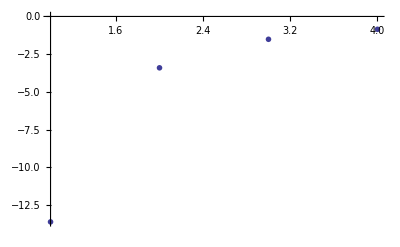

```mathematica
DiscretePlot[{EBohr[n]},{n,1,4},Axes->{False,True},PlotMarkers->{"-----",Large},Filling->None]
```

```mathematica
(*Finite Mass Correction *)
EBohrM[n_]:=-1/2 me(mp/(me+mp)) α^2 c^2 1/n^2 1/e (* in eV *)
```

```mathematica
mp/(me+mp)100
```

99.9456

```mathematica
Table[EBohrM[n],{n,1,4}]
```

{-13.5983,-3.39957,-1.51092,-0.849893}

```mathematica
Table[λ[EBohrM[m]-EBohrM[n]],{n,1,3},{m,n+1,n+4}]//TableForm
```

121.568 | 102.573 | 97.2548 | 94.9754
656.47 | 486.274 | 434.173 | 410.294
1875.63 | 1282.17 | 1094.12 | 1005.22

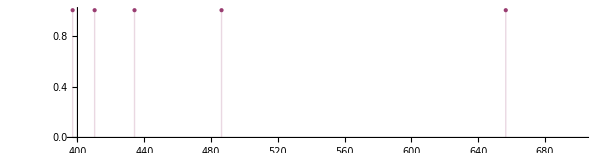

```mathematica
SpecBohrM=Table[{λ[EBohrM[m]-EBohrM[n]],1},{n,1,30},{m,n+1,n+30}];
ListPlot[SpecBohrM,Filling ->Axis,PlotRange->{{400,700},{0,1}},Axes->{True,False},AspectRatio->0.25]
```

## Fine Structure

### Relativistic coorection

```mathematica
ERel[n_,l_]:=-α^2 Abs[EBohrM[n]]( 1/(n(l+1/2))-3/(4 n^2)) 10^3(* in meV*)
```

```mathematica
N[ERel[1,0],20]
```

-0.905159

```mathematica
Table[1/n^2( n/(l+1/2)-3/4),{n,1,4},{l,0,n-1}]//TableForm
```

5/4 |  |  | 
13/16 | 7/48 |  | 
7/12 | 5/36 | 1/20 | 
29/64 | 23/192 | 17/320 | 11/448

```mathematica
LCM[64,192,320,448] 11/448
```

```mathematica
165
```

### Darwin Term

```mathematica
EDarwin[n_,L_]:=1/n α^2 Abs[EBohrM[n]] KroneckerDelta[0,L] 10^3(* in meV*)
```

```mathematica
EDarwin[2,0]
```

0.0905159

### Spin - Orbital

```mathematica
ESL[n_,j_,l_]:=If[l>0,Abs[EBohrM[n]]/2 α^2(j(j+1)-l(l+1)-3/4)/(n l(l+1/2)(l+1)),0] 10^3
```

```mathematica
(* compare same J *)
ERel[3,1]+ESL[3,1+1/2,1]
ERel[3,2]+ESL[3,2-1/2,2]
```

-0.00670488

-0.00670488

```mathematica
(* compare J=1/2 with Darwin term *)
ERel[2,0]+EDarwin[2,0]
ERel[2,1]+ESL[2,1-1/2,1]
```

-0.0565724

-0.0565724

```mathematica
Table[{{n,l+1/2,If[l>0,1/2((l+1/2)(l+3/2)-l(l+1)-3/4)/(n l(l+1/2)(l+1)),0]},{n,1-1/2,If[l>1/2,1/2((l-1/2)(l+1/2)-l(l+1)-3/4)/(n l(l+1/2)(l+1)),0]}},{n,1,4},{l,0,n-1}]//TableForm
```

1 | 1/2 | 0
1 | 1/2 | 0 |  |  | 
2 | 1/2 | 0
2 | 1/2 | 0 | 2 | 3/2 | 1/12
2 | 1/2 | -1/6 |  | 
3 | 1/2 | 0
3 | 1/2 | 0 | 3 | 3/2 | 1/18
3 | 1/2 | -1/9 | 3 | 5/2 | 1/45
3 | 1/2 | -1/30 | 
4 | 1/2 | 0
4 | 1/2 | 0 | 4 | 3/2 | 1/24
4 | 1/2 | -1/12 | 4 | 5/2 | 1/60
4 | 1/2 | -1/40 | 4 | 7/2 | 1/112
4 | 1/2 | -1/84

```mathematica
Manipulate[DiscretePlot[{ERel[n,l]+EDarwin[n,l]+ESL[n,l+1/2,l],ERel[n,l]+EDarwin[n,l]+ESL[n,l-1/2,l]},{l,0,n-1},Axes->{False,True},PlotMarkers->{"-----",Large},Filling->None],{n,1,5,1}]
```

```mathematica
Manipulate[DiscretePlot[{
EBohr[n] 10^3,
EBohr[n] 10^3+ERel[n,l],
EBohr[n] 10^3+ERel[n,l]+EDarwin[n,l]+ESL[n,l+1/2,l],EBohr[n] 10^3+ERel[n,l]+EDarwin[n,l]+ESL[n,l-1/2,l],
EBohr[n] 10^3+ERel[n,l]+EDarwin[n,l]
},{l,0,n-1},Axes->{False,True},PlotMarkers->{"-----",Large},Filling->None,PlotStyle->{Gray,Orange, Red, Blue,Green}],{n,1,5,1}]
```

```mathematica
Manipulate[DiscretePlot[{
EBohr[n] 10^3,
EBohr[n] 10^3+ERel[n,l],
EBohr[n] 10^3+ERel[n,l]+EDarwin[n,l]+ESL[n,l+1/2,l],EBohr[n] 10^3+ERel[n,l]+EDarwin[n,l]+ESL[n,l-1/2,l],
EBohr[n] 10^3+ERel[n,l]+EDarwin[n,l]
},{n,1,l+1},Axes->{False,True},PlotMarkers->{"-----",Large},Filling->None,PlotStyle->{Gray,Orange, Red, Blue,Green}],{l,0,5,1}]
```

## Energy for Fine structure

```mathematica
Efine[n_,J_]:=If[J>0,-α^2 Abs[EBohrM[n]](1/(n(J+1/2))-3/(4 n^2)),0] 10^3(* in meV*)
```

```mathematica
Efine[5,3/2]
ERel[5,1]+ESL[5,3/2,1]
```

-0.00202756

-0.00202756

```mathematica
Table[{Efine[n,l+1/2],Efine[n,l-1/2]},{n,1,3},{l,0,n-1}]//TableForm
```

-0.181032
0 |  | 
-0.0565724
0 | -0.0113145
-0.0565724 | 
-0.0201146
0 | -0.00670488
-0.0201146 | -0.00223496
-0.00670488

```mathematica
Manipulate[
DiscretePlot[{
EBohr[n]+ERel[n,l],
EBohr[n]+Efine[n,l+1/2],
EBohr[n]+Efine[n,l-1/2],
EBohr[n]
},{l,0,n-1},PlotMarkers->{"-----",Large},Filling->None,PlotStyle->{Gray,Orange, Red, Blue}]
,{n,1,7,1}]
```

## Spectrum

```mathematica
Table[{EBohrM[n]+Efine[n,l+1/2] 1/10^3,EBohrM[n]+Efine[n,l-1/2] 1/10^3},{n,1,4},{l,0,n-1}]//TableForm
```

-13.5985
-13.5983 |  |  | 
-3.39963
-3.39957 | -3.39958
-3.39963 |  | 
-1.51094
-1.51092 | -1.51093
-1.51094 | -1.51092
-1.51093 | 
-0.849902
-0.849893 | -0.849896
-0.849902 | -0.849894
-0.849896 | -0.849894
-0.849894

```mathematica
Spec[l_]:=Switch[l,0,"s",1,"p",2,"d",3,"f",4,"g"]
```

```mathematica
SpecJ[l_,j_]:=Switch[j-l,1/2,"+",-1/2,"-"]
```

```mathematica
DE[m_,n_,ll_,l_,jj_,j_]:=
If[Abs[ll-l]==1 &&1≥Abs[jj-j]≥0&& jj≥0&&j≥0&&m-n>0 ,
{ToString[m]<>ToString[Spec[ll]]<>SpecJ[ll,jj],ToString[n]<>ToString[Spec[l]]<>SpecJ[l,j]},{0,0}]
```

```mathematica
FineD=Table[If[Abs[ll-l]==1 &&1≥Abs[jj-j]≥0&& jj≥0&&j≥0&&m-n>0 ,
λ[EBohrM[m]+Efine[m,jj] 1/10^3-EBohrM[n]-Efine[n,jj] 1/10^3],0],{n,2,4},{m,n+1,31},{ll,0,m-1},{l,0,n-1},{jj,ll-1/2,ll+1/2},{j,l-1/2,l+1/2}];
ListFine=Select[Flatten[FineD],Positive];
LFineD=Length[ListFine]
SpecFine=Table[{ListFine[[n]],1},{n,1,LFineD}];
```

1080

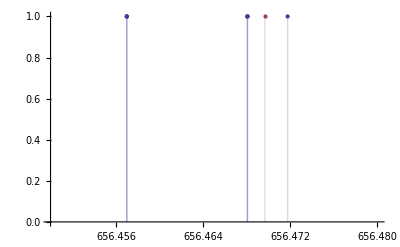

```mathematica
Show[ListPlot[SpecFine,Filling->Axis,PlotRange->{{656.45,656.48},{0,1}}],
ListPlot[Spectrum,Filling ->Axis,PlotRange->{{0,1200},{0,1}}]]
```

```mathematica
level[n_,j_]:=-1/n^2-p^2/n^2 If[j>0,(1/(n(j+1/2))-3/(4 n^2)),0]
```

```mathematica
Table[{{n,l+1/2,level[n,l+1/2]},{n,l-1/2,level[n,l-1/2]}},{n,1,4},{l,0,n-1}]//TableForm
```

1 | 1/2 | -1-p^2/4
1 | -1/2 | -1 |  |  | 
2 | 1/2 | -1/4-(5 p^2)/64
2 | -1/2 | -1/4 | 2 | 3/2 | -1/4-p^2/64
2 | 1/2 | -1/4-(5 p^2)/64 |  | 
3 | 1/2 | -1/9-p^2/36
3 | -1/2 | -1/9 | 3 | 3/2 | -1/9-p^2/108
3 | 1/2 | -1/9-p^2/36 | 3 | 5/2 | -1/9-p^2/324
3 | 3/2 | -1/9-p^2/108 | 
4 | 1/2 | -1/16-(13 p^2)/1024
4 | -1/2 | -1/16 | 4 | 3/2 | -1/16-(5 p^2)/1024
4 | 1/2 | -1/16-(13 p^2)/1024 | 4 | 5/2 | -1/16-(7 p^2)/3072
4 | 3/2 | -1/16-(5 p^2)/1024 | 4 | 7/2 | -1/16-p^2/1024
4 | 5/2 | -1/16-(7 p^2)/3072

```mathematica
Table[{level[m,3/2]-level[n,1/2],level[m,1/2]-level[n,1/2]},{m,1,4},{n,1,m-1}]//TableForm
```

|  | 
3/4+(15 p^2)/64
3/4+(11 p^2)/64 |  | 
8/9+(13 p^2)/54
8/9+(2 p^2)/9 | 5/36+(119 p^2)/1728
5/36+(29 p^2)/576 | 
15/16+(251 p^2)/1024
15/16+(243 p^2)/1024 | 3/16+(75 p^2)/1024
3/16+(67 p^2)/1024 | 7/144+(211 p^2)/9216
7/144+(139 p^2)/9216

## HyperFine Structure

### Fermi Contact

```mathematica
EFer[n_,l_,i_,f_]:=
α^2 Abs[EBohrM[n]] ge gp 2/3 me/mp If[l>0,0 ,(f(f+1)-i(i+1)-1/2(1/2+1))/n] 10^6(* in μeV*)
```

```mathematica
α^2 Abs[EBohrM[1]] ge gp 2/3 me/mp
```

2.94053×10^-6

```mathematica
EFer[2,0,1/2,0]
```

-0.551349

```mathematica
EFer[1,0,1/2,0]-EFer[1,0,1/2,1]
```

-5.88105

```mathematica
λ[(EFer[1,1,1/2,0]-EFer[1,0,1/2,0])1/10^3] 1/10^9
```

0.21082

### J - I Coupling

```mathematica
gj[l_,j_,ge_]:=If[j-l>0,1+(ge-1)/(2l+1),1-(ge-1)/(2l+1)]
Table[gj[l,j,2],{l,0,3},{j,l+1/2,l-1/2,-1}]
EJI[n_,l_,j_,f_]:=-α^2 Abs[EBohrM[n]]gj[l,j,ge]gp 1/2 me/mp If[l>0,1/(n l(l+1/2)(l+1)),0]((f(f+1)-j(j+1)-1/2(1/2+1))/2)10^6(* in μeV*)
```

{{2,0},{4/3,2/3},{6/5,4/5},{8/7,6/7}}

```mathematica
-α^2 Abs[EBohrM[1]]gj[0,1/2,ge]gp 1/2 me/mp
```

-2.2054×10^-6

### Total effect

```mathematica
EFer[n_,l_,i_,f_]:=α^2 Abs[EBohrM[n]] ge gp 2/3 me/mp If[l>0,0 ,(f(f+1)-i(i+1)-1/2(1/2+1))/n] 10^6(* in μeV*)
EJI[n_,l_,j_,f_]:=-α^2 Abs[EBohrM[n]]gj[l,j,ge]gp 1/2 me/mp If[l>0,1/(n l(l+1/2)(l+1)),0]((f(f+1)-j(j+1)-1/2(1/2+1))/2)10^6(* in μeV*)
```

```mathematica
gh[l_,j_,ge_]:=If[l>0,-gj[l,j,ge]/(2l(l+1/2)(l+1)),ge 4/3]
Table[{gh[l,l-1/2,2],gh[l,l+1/2,2]},{l,0,3}]//TableForm
```

8/3 | 8/3
-1/9 | -2/9
-2/75 | -1/25
-1/98 | -2/147

```mathematica
EHF[n_,l_,s_,j_,i_,f_]:=α^2 Abs[EBohrM[n]] gp me/mp 1/n gh[l,j,ge]((f(f+1)-j(j+1)-i(i+1))/2)10^6(* in μeV*)
```

```mathematica
λ[(EHF[1,0,1/2,1/2,1/2,1]-EHF[1,0,1/2,1/2,1/2,0])10^-6]/10^9
```

0.21082

```mathematica
f=c/(λ[(EHF[1,0,1/2,1/2,1/2,1]-EHF[1,0,1/2,1/2,1/2,0])10^-6]/10^9)
```

1.42203×10^9

```mathematica
EHF[1,0,1/2,1/2,1/2,0]
EFer[1,0,1/2,0]+EJI[1,0,1/2,0]
```

-4.41079

-4.41079

```mathematica
EHF[2,1,1/2,1/2,1/2,0]
EFer[2,1,1/2,0]
EJI[2,1,1/2,0]
EFer[2,1,1/2,0]+EJI[2,1,1/2,0]
```

0.0229197

0.

0.0229197

0.0229197

```mathematica
Table[{
{n,l,l+1/2,l+1,EHF[n,l,1/2,l+1/2,1/2,l+1]},{n,l,l+1/2,l,EHF[n,l,1/2,l+1/2,1/2,l]},
{n,l,l-1/2,l,EHF[n,l,1/2,l-1/2,1/2,l]},{n,l,l-1/2,l-1,EHF[n,l,1/2,l-1/2,1/2,l-1]}},{n,1,4},{l,0,n-1}]//TableForm
```

1 | 0 | 1/2 | 1 | 1.47026
1 | 0 | 1/2 | 0 | -4.41079
1 | 0 | -1/2 | 0 | -1.47026
1 | 0 | -1/2 | -1 | -1.47026 |  |  | 
2 | 0 | 1/2 | 1 | 0.183783
2 | 0 | 1/2 | 0 | -0.551349
2 | 0 | -1/2 | 0 | -0.183783
2 | 0 | -1/2 | -1 | -0.183783 | 2 | 1 | 3/2 | 2 | -0.0459191
2 | 1 | 3/2 | 1 | 0.0765319
2 | 1 | 1/2 | 1 | -0.00763988
2 | 1 | 1/2 | 0 | 0.0229197 |  | 
3 | 0 | 1/2 | 1 | 0.0544542
3 | 0 | 1/2 | 0 | -0.163363
3 | 0 | -1/2 | 0 | -0.0544542
3 | 0 | -1/2 | -1 | -0.0544542 | 3 | 1 | 3/2 | 2 | -0.0136057
3 | 1 | 3/2 | 1 | 0.0226761
3 | 1 | 1/2 | 1 | -0.00226367
3 | 1 | 1/2 | 0 | 0.00679101 | 3 | 2 | 5/2 | 3 | -0.00408091
3 | 2 | 5/2 | 2 | 0.00571328
3 | 2 | 3/2 | 2 | -0.00163079
3 | 2 | 3/2 | 1 | 0.00271798 | 
4 | 0 | 1/2 | 1 | 0.0229729
4 | 0 | 1/2 | 0 | -0.0689186
4 | 0 | -1/2 | 0 | -0.0229729
4 | 0 | -1/2 | -1 | -0.0229729 | 4 | 1 | 3/2 | 2 | -0.00573989
4 | 1 | 3/2 | 1 | 0.00956649
4 | 1 | 1/2 | 1 | -0.000954986
4 | 1 | 1/2 | 0 | 0.00286496 | 4 | 2 | 5/2 | 3 | -0.00172163
4 | 2 | 5/2 | 2 | 0.00241029
4 | 2 | 3/2 | 2 | -0.000687989
4 | 2 | 3/2 | 1 | 0.00114665 | 4 | 3 | 7/2 | 4 | -0.000819747
4 | 3 | 7/2 | 3 | 0.00105396
4 | 3 | 5/2 | 3 | -0.000438853
4 | 3 | 5/2 | 2 | 0.000614394

## Total Energy Level

```mathematica
Etot[n_,l_,j_,f_]:=If[j<0,EBohrM[n] 10^3,EBohrM[n] 10^3+Efine[n,j]+EHF[n,l,1/2,j,1/2,f] 1/10^3](* in meV *)
```

```mathematica
Table[{
{n,"","","Bohr",EBohrM[n] 10^3},
{n,l,l+1/2,"Fine ↑",EBohrM[n] 10^3+Efine[n,l+1/2]},
{n,l,l+1/2,l+1,-Etot[n,l,l+1/2,l+1]},{n,l,l+1/2,l,-Etot[n,l,l+1/2,l]},
{n,l,l+1/2,"Fine ↓",EBohrM[n] 10^3+Efine[n,l-1/2]},
{n,l,l-1/2,l,-Etot[n,l,l-1/2,l]},{n,l,l-1/2,l-1,-Etot[n,l,l-1/2,l-1]}},{n,1,4},{l,0,n-1}]//TableForm
```

1 |  |  | Bohr | -13598.3
1 | 0 | 1/2 | Fine ↑ | -13598.5
1 | 0 | 1/2 | 1 | 13598.5
1 | 0 | 1/2 | 0 | 13598.5
1 | 0 | 1/2 | Fine ↓ | -13598.3
1 | 0 | -1/2 | 0 | 13598.3
1 | 0 | -1/2 | -1 | 13598.3 |  |  | 
2 |  |  | Bohr | -3399.57
2 | 0 | 1/2 | Fine ↑ | -3399.63
2 | 0 | 1/2 | 1 | 3399.63
2 | 0 | 1/2 | 0 | 3399.63
2 | 0 | 1/2 | Fine ↓ | -3399.57
2 | 0 | -1/2 | 0 | 3399.57
2 | 0 | -1/2 | -1 | 3399.57 | 2 |  |  | Bohr | -3399.57
2 | 1 | 3/2 | Fine ↑ | -3399.58
2 | 1 | 3/2 | 2 | 3399.58
2 | 1 | 3/2 | 1 | 3399.58
2 | 1 | 3/2 | Fine ↓ | -3399.63
2 | 1 | 1/2 | 1 | 3399.63
2 | 1 | 1/2 | 0 | 3399.63 |  | 
3 |  |  | Bohr | -1510.92
3 | 0 | 1/2 | Fine ↑ | -1510.94
3 | 0 | 1/2 | 1 | 1510.94
3 | 0 | 1/2 | 0 | 1510.94
3 | 0 | 1/2 | Fine ↓ | -1510.92
3 | 0 | -1/2 | 0 | 1510.92
3 | 0 | -1/2 | -1 | 1510.92 | 3 |  |  | Bohr | -1510.92
3 | 1 | 3/2 | Fine ↑ | -1510.93
3 | 1 | 3/2 | 2 | 1510.93
3 | 1 | 3/2 | 1 | 1510.93
3 | 1 | 3/2 | Fine ↓ | -1510.94
3 | 1 | 1/2 | 1 | 1510.94
3 | 1 | 1/2 | 0 | 1510.94 | 3 |  |  | Bohr | -1510.92
3 | 2 | 5/2 | Fine ↑ | -1510.92
3 | 2 | 5/2 | 3 | 1510.92
3 | 2 | 5/2 | 2 | 1510.92
3 | 2 | 5/2 | Fine ↓ | -1510.93
3 | 2 | 3/2 | 2 | 1510.93
3 | 2 | 3/2 | 1 | 1510.93 | 
4 |  |  | Bohr | -849.893
4 | 0 | 1/2 | Fine ↑ | -849.902
4 | 0 | 1/2 | 1 | 849.902
4 | 0 | 1/2 | 0 | 849.902
4 | 0 | 1/2 | Fine ↓ | -849.893
4 | 0 | -1/2 | 0 | 849.893
4 | 0 | -1/2 | -1 | 849.893 | 4 |  |  | Bohr | -849.893
4 | 1 | 3/2 | Fine ↑ | -849.896
4 | 1 | 3/2 | 2 | 849.896
4 | 1 | 3/2 | 1 | 849.896
4 | 1 | 3/2 | Fine ↓ | -849.902
4 | 1 | 1/2 | 1 | 849.902
4 | 1 | 1/2 | 0 | 849.902 | 4 |  |  | Bohr | -849.893
4 | 2 | 5/2 | Fine ↑ | -849.894
4 | 2 | 5/2 | 3 | 849.894
4 | 2 | 5/2 | 2 | 849.894
4 | 2 | 5/2 | Fine ↓ | -849.896
4 | 2 | 3/2 | 2 | 849.896
4 | 2 | 3/2 | 1 | 849.896 | 4 |  |  | Bohr | -849.893
4 | 3 | 7/2 | Fine ↑ | -849.894
4 | 3 | 7/2 | 4 | 849.894
4 | 3 | 7/2 | 3 | 849.894
4 | 3 | 7/2 | Fine ↓ | -849.894
4 | 3 | 5/2 | 3 | 849.894
4 | 3 | 5/2 | 2 | 849.894

```mathematica
Table[{
{n,l,l+1/2,"Fine ↑",Efine[n,l+1/2]/(EBohrM[n] 10^3)10^6},
{n,l,l+1/2,l+1,(Etot[n,l,l+1/2,l+1]/(EBohrM[n] 10^3)-1)10^6},{n,l,l+1/2,l,(Etot[n,l,l+1/2,l]/(EBohrM[n] 10^3)-1)10^6},
{n,l,l+1/2,"Fine ↓",(Efine[n,l-1/2]/(EBohrM[n] 10^3))10^6},
{n,l,l-1/2,l,(Etot[n,l,l-1/2,l]/(EBohrM[n] 10^3)-1)10^6},{n,l,l-1/2,l-1,(Etot[n,l,l-1/2,l-1]/(EBohrM[n] 10^3)-1)10^6}},{n,1,4},{l,0,n-1}]//TableForm
```

1 | 0 | 1/2 | Fine ↑ | 13.3128
1 | 0 | 1/2 | 1 | 13.2047
1 | 0 | 1/2 | 0 | 13.6372
1 | 0 | 1/2 | Fine ↓ | 0.
1 | 0 | -1/2 | 0 | 0.
1 | 0 | -1/2 | -1 | 0. |  |  | 
2 | 0 | 1/2 | Fine ↑ | 16.641
2 | 0 | 1/2 | 1 | 16.587
2 | 0 | 1/2 | 0 | 16.8032
2 | 0 | 1/2 | Fine ↓ | 0.
2 | 0 | -1/2 | 0 | 0.
2 | 0 | -1/2 | -1 | 0. | 2 | 1 | 3/2 | Fine ↑ | 3.32821
2 | 1 | 3/2 | 2 | 3.34172
2 | 1 | 3/2 | 1 | 3.3057
2 | 1 | 3/2 | Fine ↓ | 16.641
2 | 1 | 1/2 | 1 | 16.6433
2 | 1 | 1/2 | 0 | 16.6343 |  | 
3 | 0 | 1/2 | Fine ↑ | 13.3128
3 | 0 | 1/2 | 1 | 13.2768
3 | 0 | 1/2 | 0 | 13.421
3 | 0 | 1/2 | Fine ↓ | 0.
3 | 0 | -1/2 | 0 | 0.
3 | 0 | -1/2 | -1 | 0. | 3 | 1 | 3/2 | Fine ↑ | 4.43761
3 | 1 | 3/2 | 2 | 4.44662
3 | 1 | 3/2 | 1 | 4.4226
3 | 1 | 3/2 | Fine ↓ | 13.3128
3 | 1 | 1/2 | 1 | 13.3143
3 | 1 | 1/2 | 0 | 13.3083 | 3 | 2 | 5/2 | Fine ↑ | 1.4792
3 | 2 | 5/2 | 3 | 1.48191
3 | 2 | 5/2 | 2 | 1.47542
3 | 2 | 5/2 | Fine ↓ | 4.43761
3 | 2 | 3/2 | 2 | 4.43869
3 | 2 | 3/2 | 1 | 4.43581 | 
4 | 0 | 1/2 | Fine ↑ | 10.8167
4 | 0 | 1/2 | 1 | 10.7897
4 | 0 | 1/2 | 0 | 10.8978
4 | 0 | 1/2 | Fine ↓ | 0.
4 | 0 | -1/2 | 0 | 0.
4 | 0 | -1/2 | -1 | 0. | 4 | 1 | 3/2 | Fine ↑ | 4.16026
4 | 1 | 3/2 | 2 | 4.16702
4 | 1 | 3/2 | 1 | 4.14901
4 | 1 | 3/2 | Fine ↓ | 10.8167
4 | 1 | 1/2 | 1 | 10.8178
4 | 1 | 1/2 | 0 | 10.8133 | 4 | 2 | 5/2 | Fine ↑ | 1.94146
4 | 2 | 5/2 | 3 | 1.94348
4 | 2 | 5/2 | 2 | 1.93862
4 | 2 | 5/2 | Fine ↓ | 4.16026
4 | 2 | 3/2 | 2 | 4.16107
4 | 2 | 3/2 | 1 | 4.15891 | 4 | 3 | 7/2 | Fine ↑ | 0.832052
4 | 3 | 7/2 | 4 | 0.833017
4 | 3 | 7/2 | 3 | 0.830812
4 | 3 | 7/2 | Fine ↓ | 1.94146
4 | 3 | 5/2 | 3 | 1.94197
4 | 3 | 5/2 | 2 | 1.94073

```mathematica
Manipulate[
DiscretePlot[{
EBohrM[n] 10^3,
EBohrM[n] 10^3+Efine[n,l+1/2],
EBohrM[n] 10^3+Efine[n,l-1/2],
Etot[n,l,l+1/2,l+1],
Etot[n,l,l+1/2,l],
Etot[n,l,l-1/2,l],
Etot[n,l,l-1/2,l-1]
},{l,0,n-1},PlotMarkers->{"-----",Large},Filling->None,PlotStyle->{Black,Pink, Red,Green, Blue,Purple,Orange},AspectRatio->10,ImageSize->200]
,{n,1,7,1}]
```

## Total Spectrum

```mathematica
λBohrM=Table[λ[EBohrM[m]-EBohrM[n]],{n,1,4},{m,n+1,n+30}];
ListλBohrM=Select[Flatten[λBohrM],Positive];
LλBohrM=Length[ListλBohrM]
SpecBohrM=Table[{ListλBohrM[[n]],1},{n,1,LλBohrM}];
```

120

```mathematica
λFine=Table[If[Abs[ll-l]==1 &&1≥Abs[jj-j]≥0&& jj≥0&&j≥0&&m-n>0 ,
λ[EBohrM[m]+Efine[m,jj] 1/10^3-EBohrM[n]-Efine[n,jj] 1/10^3],0],{n,2,4},{m,n+1,31},{ll,0,m-1},{l,0,n-1},{jj,ll-1/2,ll+1/2},{j,l-1/2,l+1/2}];
ListλFine=Select[Flatten[λFine],Positive];
LλFine=Length[ListλFine]
SpecFine=Table[{ListλFine[[n]],1},{n,1,LλFine}];
```

1080

```mathematica
λHF=Table[If[Abs[ll-l]==1 &&1≥Abs[jj-j]≥0&& jj≥0&&j≥0&&m-n>0 ,
λ[(Etot[m,ll,jj,ff]-Etot[n,l,j,f])1/10^3],0],{n,2,4},{m,n+1,31},{ll,0,m-1},{l,0,n-1},{jj,ll-1/2,ll+1/2},{j,l-1/2,l+1/2},{ff,jj-1/2,jj+1/2},{f,j-1/2,j+1/2}];
ListλHF=Select[Flatten[λHF],Positive];
LλHF=Length[ListλHF]
SpecHF=Table[{ListλHF[[n]],1},{n,1,LλHF}];
```

4320

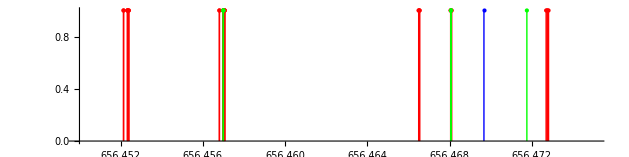

```mathematica
Show[
ListPlot[SpecHF,Filling->Axis,PlotRange->{{656.45,656.475},{0,1}},PlotStyle->Red,FillingStyle->Red,Axes->{True,False},AspectRatio->0.25],
ListPlot[SpecFine,Filling->Axis,PlotRange->{{656.45,656.48},{0,1}},PlotStyle->Green,FillingStyle->Green],
ListPlot[SpecBohrM,Filling ->Axis,PlotRange->{{0,1200},{0,1}},PlotStyle->Blue,FillingStyle->Blue]]
```

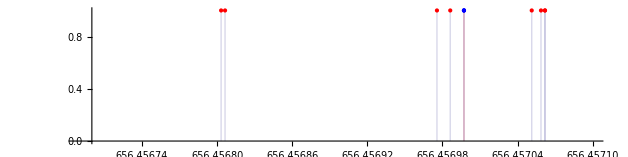

```mathematica
ListPlot[{SpecHF,SpecFine},Filling->Axis,PlotRange->{{656.45669,656.4571},{0,1}},PlotStyle->{Red,Blue},Axes->{True,False},AspectRatio->0.25]
```